## lognormal

```mathematica
f0=10^-2.69;
m10=30;
m20=10;
mc0=16.26;
σc0=0.75;
```

## mass function

```mathematica
Plog[i_,mc_,σc_]:=1/(√(2*π)*σc*i)*ⅇ^(-(Log[i/mc])^2/(2*σc^2));
Integrate[Plog[ii,mc,σc],{ii,0,∞},Assumptions->mc>1&&σc>0]
```

1

## m_pbh

```mathematica
1/Integrate[Plog[ii,mc,σc]/ii,{ii,0,∞},Assumptions->mc>1&&σc>0]
mpbh[mc_,σc_]:=ⅇ^(-σc^2/2) mc
```

ⅇ^(-σc^2/2) mc

## F(m)

```mathematica
F[i_,mc_,σc_]:=Plog[i,mc,σc]*mpbh[mc,σc]/i;
F[ii,mc,σc]
Integrate[F[ii,mc,σc],{ii,0,∞},Assumptions->mc>1&&σc>0]
```

(ⅇ^(-σc^2/2-Log[ii/mc]^2/(2 σc^2)) mc)/(ii^2 √(2 π) σc)

1

## R1

```mathematica
Integrate[l^(-21/37)F[l,mc,σc],{l,0,∞},Assumptions->mc>1&&σc>0]
```

(ⅇ^((1995 σc^2)/2738))/mc^(21/37)

```mathematica
1.32*10^6*(f/mpbh[mc,σc])^(53/37)(ⅇ^((1995 σc^2)/2738))/mc^(21/37)*(i*j)^(3/37)*(i+j)^(36/37)F[i,mc,σc]*F[j,mc,σc]
```

(210085. ⅇ^(-(743 σc^2)/2738-Log[i/mc]^2/(2 σc^2)-Log[j/mc]^2/(2 σc^2)) (i j)^(3/37) (i+j)^(36/37) ((ⅇ^(σc^2/2) f)/mc)^(53/37) mc^(53/37))/(i^2 j^2 σc^2)

```mathematica
Clear[i,mergerRateDensity1st]
mergerRateDensity1st[f_,i_,j_,mc_,σc_]:=1/(i^2 j^2 σc^2)210084.52488130186 ⅇ^(-(743 σc^4+1369 Log[i/mc]^2+1369 Log[j/mc]^2)/(2738 σc^2)) (i j)^(3/37) (i+j)^(36/37) ((ⅇ^(σc^2/2) f)/mc)^(53/37) mc^(53/37);
mergerRateDensity1st[f0,m10,m20,mc0,σc0]
```

0.0249471

## R2

```mathematica
(*Clear[normalFactorMergerRateDensity1st,normalizedMergerRateDensity1st];
normalFactorMergerRateDensity1st[f_?NumericQ,mc_?NumericQ,σc_?NumericQ]:=NIntegrate[mergerRateDensity1st[f,m1,m2,mc,σc],{m1,0,∞},{m2,0,∞},PrecisionGoal->3];

normalizedMergerRateDensity1st[f_,i_,j_,α_,M_]:=mergerRateDensity1st[f,i,j,α,M]/normalFactorMergerRateDensity1st[f,α,M];
normalFactorMergerRateDensity1st[f0,mc0,σc0]
normalizedMergerRateDensity1st[f0,m10,m20,mc0,σc0]
NIntegrate[normalizedMergerRateDensity1st[f0,m1,m2,mc0,σc0],{m1,0,∞},{m2,0,∞},PrecisionGoal->3]*)
```

```mathematica
mergerRateDensity2nd00[f_,i_,j_,k_,l_,mc_,σc_]:=1.59*10^4*(f/mpbh[mc,σc])^(69/37)k^(6/37)l^(-42/37)(i+j)^(6/37)(i+j+k)^(72/37)F[i,mc,σc]*F[j,mc,σc]*F[k,mc,σc]*F[l,mc,σc]

mergerRateDensity2nd00[f,i,j,k,l,mc,σc]
```

(402.752 ⅇ^(-2 σc^2-Log[i/mc]^2/(2 σc^2)-Log[j/mc]^2/(2 σc^2)-Log[k/mc]^2/(2 σc^2)-Log[l/mc]^2/(2 σc^2)) (i+j)^(6/37) (i+j+k)^(72/37) ((ⅇ^(σc^2/2) f)/mc)^(69/37) mc^4)/(i^2 j^2 k^(68/37) l^(116/37) σc^4)

```mathematica
Integrate[mergerRateDensity2nd00[f,i-e,e,j,l,mc,σc],{l,0,∞},Assumptions->mc>1&&σc>0]
```

(1009.55 ⅇ^(-(-3318 σc^4+1369 Log[e/mc]^2+1369 Log[(-e+i)/mc]^2+1369 Log[j/mc]^2)/(2738 σc^2)) f^(69/37) i^(6/37) (i+j)^(72/37))/(e^2 (-1. e+i)^2 j^(68/37) σc^3)

```mathematica
mergerRateDensity2nd0[f_?NumericQ,i_?NumericQ,j_?NumericQ,e_?NumericQ,mc_?NumericQ,σc_?NumericQ]:=(1009.5488113544313 ⅇ^(-(-3318 σc^4+1369 Log[e/mc]^2+1369 Log[(-e+i)/mc]^2+1369 Log[j/mc]^2)/(2738 σc^2)) f^(69/37) i^(6/37) (i+j)^(72/37))/(e^2 (-1. e+i)^2 j^(68/37) σc^3)
```

```mathematica
e0=0.5;
mergerRateDensity2nd0[f0,m10,m20,e0,mc0,σc0]
```

2.80198×10^-6

```mathematica
Integrate[(ⅇ^(-(1369 Log[e/mc]^2+1369 Log[(-e+i)/mc]^2)/(2738 σc^2)))/(e^2 (-1. e+i)^2),e]
```

∫(ⅇ^(-(1369 Log[e/mc]^2+1369 Log[(-e+i)/mc]^2)/(2738 σc^2)))/(e^2 (-1. e+i)^2)ⅆe

```mathematica
mergerRateDensity2nd1[f_?NumericQ,i_?NumericQ,j_?NumericQ,mc_?NumericQ,σc_?NumericQ]:=(1009.5488113544313  f^(69/37)i^(6/37) (i+j)^(72/37))/(j^(68/37) σc^3)ⅇ^(-(-3318 σc^4+1369 Log[j/mc]^2)/(2738 σc^2))NIntegrate[(ⅇ^(-(1369 Log[e/mc]^2+1369 Log[(-e+i)/mc]^2)/(2738 σc^2)))/(e^2 (-1. e+i)^2),{e,0,i},PrecisionGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]
```

```mathematica
mergerRateDensity2nd1[f0,m10,m20,mc0,σc0]//Timing
```

{0.00083,0.000716225}

```mathematica
mergerRateDensity2nd[f0,m10,m20,mc0,σc0]//Timing
```

{0.001319,0.000939191}

```mathematica
Clear[mergerRateDensity2nd];
mergerRateDensity2nd[f_?NumericQ,i_?NumericQ,j_?NumericQ,mc_?NumericQ,σc_?NumericQ]:=1/2(mergerRateDensity2nd1[f,i,j,mc,σc]+mergerRateDensity2nd1[f,j,i,mc,σc])
```

```mathematica
Clear@mergerRateDensity;
mergerRateDensity[f_?NumericQ,i_?NumericQ,j_?NumericQ,mc_?NumericQ,σc_?NumericQ]:=If[i≥j,mergerRateDensity1st[f,i,j,mc,σc]+mergerRateDensity2nd[f,i,j,mc,σc],mergerRateDensity[f,j,i,mc,σc]];

mergerRateDensity[f0,m10,m20,mc0,σc0]//AbsoluteTiming
NIntegrate[mergerRateDensity[f0,m1,m2,mc0,σc0],{m1,mMin,mMax},{m2,mMin,mMax},PrecisionGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]//AbsoluteTiming
```

{0.001188,0.0195009}

{0.629888,91.6231}

```mathematica
Clear@R0;
R0[f_?NumericQ,mc_?NumericQ,σc_?NumericQ]:=R0[f,mc,σc]=NIntegrate[mergerRateDensity[f,m1,m2,mc,σc],{m1,mMin,mMax},{m2,mMin,mMax},PrecisionGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]
R0[f0,mc0,σc0]//AbsoluteTiming
```

{0.633823,91.6231}

```mathematica
ratioR[f_?NumericQ,i_?NumericQ,j_?NumericQ,mc_?NumericQ,σc_?NumericQ]:=mergerRateDensity2nd[f,i,j,mc,σc]/mergerRateDensity1st[f,i,j,mc,σc];
```

```mathematica
R1=NIntegrate[mergerRateDensity1st[f0,m1,m2,mc0,σc0],{m1,mMin,mMax},{m2,mMin,mMax},PrecisionGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]
R2=NIntegrate[mergerRateDensity2nd[f0,m1,m2,mc0,σc0],{m1,mMin,mMax},{m2,mMin,mMax},PrecisionGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]

R2/R1
```

49.1292

1.49723

0.0304753

```mathematica
ratioR[f_?NumericQ,i_?NumericQ,j_?NumericQ,mc_?NumericQ,σc_?NumericQ]:=mergerRateDensity2nd[f,i,j,mc,σc]/mergerRateDensity1st[f,i,j,mc,σc];
```

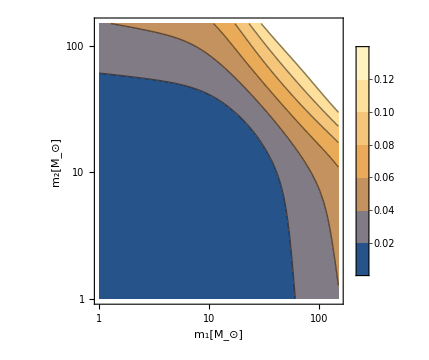

```mathematica
mMin=1;
mMax=150;

ContourPlot[ratioR[f0,i,j,mc0,σc0],{i,mMin,mMax},{j,mMin,mMax},FrameLabel->{"m_1[M_⊙]","m_2[M_⊙]"},ScalingFunctions->{"Log","Log"},FrameStyle->FontFamily->"Times",BaseStyle->FontSize->14,LabelStyle->GrayLevel[0],Frame->True,Axes->False,PlotRangePadding->None,ImageSize->360,AspectRatio->1,PlotLegends->Automatic]
(*Export["../latex/ratio-log.pdf",%]*)
```

```mathematica
Plot3D[{mergerRateDensity1st[f0,i,j,mc0,σc0]},{i,mMin,mMax},{j,mMin,mMax},PlotRange->All]
```

-Graphics3D-

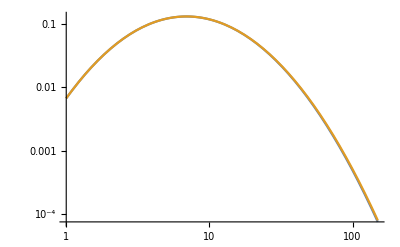

```mathematica
LogLogPlot[{mergerRateDensity1st[f0,10,j,mc0,σc0],mergerRateDensity1st[f0,10,j,mc0,σc0]+mergerRateDensity2nd[f0,10,j,mc0,σc0]},{j,mMin,150},PlotRange->All]
```